```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/eric/git/QEA-boat2/Mathematica code

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
nPoints=200000;
```

```mathematica
ClearAll[cob];
cobinner[region_,angle_,waterHeight_]:=Module[{nangle,pts,centroid},
nangle=Normalize[angle];
pts=myRandomPoint[region,nPoints];
underwaterPts=Cases[pts,pt_/;nangle.pt<waterHeight];
centroid=Total[underwaterPts]/Length[underwaterPts]
]

cob[region_,angle_,desiredVolume_]:=Module[{waterHeight},
waterHeight=waterline[region,angle,desiredVolume];
cobinner[region,angle,waterHeight]
]

rightingMoment[cob_,com_,up_,front_]:=Module[{left,r},
left = Normalize[up×front];
r=cob-com;
r.left
]

rightingArm[region_,com_,θ_,desiredVolume_,front_]:=Module[{up},
up=RotationMatrix[θ,front].{0,0,1};
rightingMoment[cob[region,up,desiredVolume],com,up,front]
]
```

```mathematica
rightingArm[boat_,front_,θ_]:=Module[{up,desiredVolume},
up=RotationMatrix[θ,front].{0,0,1};
desiredVolume=totalMass[boat];
rightingMoment[cob[region/.boat,up,desiredVolume],massCOM[boat],up,front]
]
```

```mathematica
Volume[region/.boat]
```

371.26

```mathematica
rightingArm[boat,{0,1,0},0]
```

-0.0739452

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

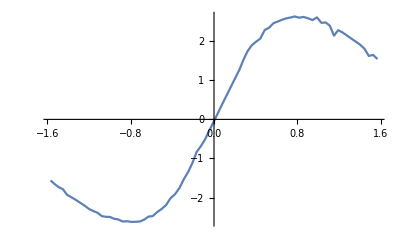

```mathematica
Plot[rightingArm[boat,{0,1,0},θ],{θ,-Pi/2,Pi/2},PlotPoints->20,MaxRecursion->2]
```

```mathematica
x=-0.2
rightingMoment[cob[boat,Normalize@{0,x,1},10000],com,Normalize@{0,x,1},{1,0,0}]
```

-0.2

0.983525

```mathematica
cob[boat,Normalize@{0,1,1},10000]
```

{0.00931387,-12.5304,7.50866}

```mathematica
Graphics3D@Hyperplane[Normalize@{0,1,1},1]
```

-Graphics3D-

```mathematica
showWaterline[boat,Normalize@{0,3,-1},2]
```

-Graphics3D-

```mathematica
Opacity
```